#### Advanced Section: Bouncing into a Spring

This looks like a great problem, but there is almost certainly something wrong with the solution because:
1. The displacement from the center of mass frame position of A (z_A[t]) should be a simple Sin[ω t] with no Cos[ω t] component
2. The final answer for Δ,L was hideous and impossible to get without Mathematica
Figure out what is wrong and then include that problem here

Example
Two particles, A and B, each of which have mass m, are connected by a massless spring with spring constant k and equilibrium length L_0. Initially, A and B are at rest at positions x_A=0 and x_B=L_0. At time t=0, a third particle C with mass m and initial velocity v_0 collides elastically with A. Assume that the motions in the problem are all one dimensional.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

1. What are the velocities of A, B, C, and the center-of-mass of the A-B system (i.e. the midpoint of the spring) immediately after the collision?
2. Write down equations for the displacements of A, B, and the center of mass of the A-B system as a function of time. Assume that A does not undergo a second collision with C and that the amplitude Δ,L of the oscillation, defined as the maximum amount that the spring is ever stretched or compressed from L_0, does not exceed L_0 (so that A and B never touch).
3. Find the angular frequency ω and the amplitude Δ,L of the oscillation of the A-B pair after the collision.

Solutions
1. Since A and C have the same mass, right after the collision they will exchange velocities and

v_A=v_0

v_C=0

Although A instantaneously picks up this new velocity, it does not move during the collision, and hence it does not transfer any impulse onto B, so that

v_B=0

This implies that the center of mass of the A-B system has velocity

v_(A-B)=v_0/2

Another way to confirm this final result is to consider the A-B system as a single object of mass 2m. This object is initially at rest, and after collision with C it picks up the velocity given by

m v_0=(2m)v_(A-B)

confirming what we found above.

2. Denote the displacement of A by x_A and the displacement of B by x_B. We start by analyzing the A-B system, consisting of A, B, and their connecting spring. After the collision, there is no external force acting upon this system (the spring force is internal), and therefore the center of mass moves at a constant velocity. By integrating, we find that the center of mass (which at time 0 resides at x=L_0/2) equals

x_(A-B)=1/2 L_0+v_(A-B)t=1/2 L_0+1/2 v_0 t

Since A and B have the same mass and the spring is massless, the center of mass of the A-B system is the midpoint of the spring, x_(A-B)=(x_A+x_B)/2, so the above equation provides a constraint for the displacements of A and B,

(x_A+x_B)/2=L_0/2+1/2 v_0 t

x_A+x_B=L_0+v_0 t

Now we analyze the motions of A and B separately. In fact, we only need to analyze the motion of A, because Equation (TextNumbered) will then fix the motion of B relative to A. The sum of the forces on A are

m (ẍ)_A=-k (x_A-x_B)

Substituting in x_B from Equation (TextNumbered),

m (ẍ)_A=-k (2 x_A-L_0-v_0 t)

Note that this equation is greatly simplified if we change to a new variable z_A defined by

x_A=z_A+1/2 L_0+1/2 v_0 t

What does this transformation physically correspond to? From Equation (TextNumbered), we see that z_A represents the displacement of A in the frame of the center of mass of the A-B system! z_A has the time derivatives

(ẋ)_A=(ż)_A+1/2 v_0

(ẍ)_A=(z̈)_A

Substituting back into Equation (TextNumbered), the differential equation governing the system becomes

m (z̈)_A=-2k z_A

This should seem very familiar - it is the equation of a simple harmonic oscillator with frequency

ω^2=2 k/m

Therefore, the displacement of A has the form

z_A[t]=c_1 Cos[ω t]+c_2 Sin[ω t]

about the center of mass of the A-B system and has the form

x_A[t]=1/2 L_0+1/2 v_0 t+c_1 Cos[ω t]+c_2 Sin[ω t]

about the lab frame. We now need to substitute in the initial conditions - right after the collision A has displacement

x_A[0]=0

and velocity

(ẋ)_A[0]=v_0

The first condition implies

0=1/2 L_0+c_1

c_1=-1/2 L_0

while the second implies

v_0=1/2 v_0+c_2 ω

c_2=1/2 v_0/ω

Therefore, the displacement of A after the collision is given by

x_A[t]=1/2 L_0+1/2 v_0 t-1/2 L_0 Cos[ω t]+1/2 v_0/ω Sin[ω t]
=1/2 L_0 (1-Cos[ω t])+1/2 v_0 (t+1/ω Sin[ω t])

Finally, we use Equation (TextNumbered) to determine the displacement of B after the collision, namely,

x_B[t]=L_0+v_0 t-x_A[t]
=1/2 L_0 (1+Cos[ω t])+1/2 v_0 (t-1/ω Sin[ω t])

Note that in the A-B center of mass frame, the motion of the system is exceedingly simple: A and B oscillate symmetrically about the center of the spring with frequency ω.

3. We already found above that the frequency of oscillation of the A-B pair is given by ω=(2 k/m)^(1/2). The magnitude Δ,L of the oscillation is given by the maximum value of

L_0-(x_B-x_A)

which can be solved using Mathematica to obtain

Δ,L=L_0-((k L_0^2-1/2 m v_0^2)/({k (k L_0^2+1/2 m v_0^2)}^(1/2)))

# Lecture 17 - Gyroscopes

### A Puzzle...

We have seen throughout class that the center of mass is a very powerful tool for evaluating systems. However, don’t let yourself get carried away with how useful it can be!

Give a counter-example to the following incorrect statement:
The gravitational force from an extended body of mass M equals the gravitational force from a point mass M located at the center of mass.

Solution
Truthfully, you would be hard pressed to find an instance where the above statement is correct. As a simple counter-example in 2D, consider the case of a mass m at (1,0) and another mass m at (-1,0). If we put another mass exactly between them, then the gravitational force on this mass would be zero (the contributions from both masses would exactly cancel). However, the gravitational force from a mass 2m at their center would certainly not be zero at this point (it would be infinite!)

Another very famous counter-example is the spherical shell of mass M, radius R, and uniform mass density. A well known fact (and one that we prove below in the section "Gravity in a Spherical Shell" below) is that the gravitational force from this spherical shell inside the shell is exactly zero at all points! This remarkable fact leads to an easy counter-example, since the actual gravitational force inside the shell is zero, while the gravitational force from a point mass m located at its center would not be zero.

### Gyroscopes

Gyroscopes...are really cool!

As was hinted earlier in the course, gyroscopes are one of the awesome phenomena (along with rolling cones, bicycles, etc.) that occur when we let the direction of angular momentum change in

τ⃗=(ⅆ L⃗)/ⅆt

These ideas will be delved into much more deeply in junior level Classical Mechanics. Let me give one more example to whet your appetite.

Try spinning a tennis racket (or a book, etc.) about the axis of its handle (shown on the left in the figure below). If you start it off straight, it will rotate very nicely. However, if you try  rotating the tennis racket as shown on the right in the figure below, you will never be able to get it spinning nicely. This awesome idea known as the Tennis Racket Theorem. (Here are links to a slow motion video and to this effect seen in zero gravity.)

```mathematica
centerPlot@-Graphics-
```

-Graphics-

### Problems

#### Projectile Motion

A ball is thrown at speed v from zero height on level ground. At what angle should it be thrown so that the area under the trajectory is maximum?

#### Falling Stick

A massless stick of length b has one end attached to a pivot and the other end glued perpendicularly to the middle of a stick of mass m and length l.
1. If the two sticks are held in a horizontal plane and then released, what is the initial acceleration of the center of mass?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

2. If the two sticks are held in a vertical plane and then released, what is the initial acceleration of the center of mass?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

#### Escape Velocity

1. A rocket is shot radially outwards away from Earth. What would its initial velocity need to be for it to escape out to r=∞? 
2. What is the escape velocity if the rocket is shot tangentially from the surface of the Earth?

#### Normal Modes

Two masses m are each connected to a wall by a spring with spring constant k. The two masses are connected to each other by a spring with spring constant k'. Initially, all springs are unstretched and the masses are at rest. While the general motion of this system can be very complicated, there are two very simple motions that we can easily analyze.
1. If both masses are shifted to the right by a distance A and then released from rest, what is the frequency of the resulting oscillation?
2. If the left mass is shifted right by a distance A and the right mass is shifted left by a distance A, what is the frequency of the resulting oscillation?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

#### A Different Potential

A particle of mass m moves in a radial potential given by V[r]=β r^k with angular momentum L. Find the radius of circular orbit in terms of L,m,k,and β.

#### Advanced Section: Crazy Chain

A frictionless planar curve is in the shape of an arbitrary function which has its endpoints at the same height but is otherwise arbitrary. A chain of uniform mass per unit length  rests on the curve from end to end, as shown below. We want to find out for what curves the chain will not move.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Let the curve be described by the function f[x], and let it run from x=a to x=b. Consider a little piece of the chain between x and x+ⅆx shown below.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

1. Using the uniform mass density ρ and the Pythagorean theorem, find the mass of the small segment of chain shown above. Leave your answer in terms of ⅆx and f'[x].

Gravity alone will determine whether the chain slides or not (see the note below), so we will calculate the net gravitational force of the chain along the curve by considering the component of gravity parallel to the plane for each segment of the chain.

2. Using the mass from Part 1, determine the gravitational force on the small segment of chain. Define positive in the direction along the curve going from a to b. Express your answer in terms of ρ, ⅆx, and f'[x].
Hint: You may find the trig relation Sin[θ]=f'[x]/((1+f'[x]^2)^(1/2)) useful.
3. Find the total gravitational force of the chain along the curve by integrating over all small segments from x=a to x=b. Use the resulting relation to describe (in words, not equations) for what planar curves f[x] the chain will be motionless.

#### Advanced Section: Inelastic Collisions from Multiple Perspectives

A massless string of length 2l connects two hockey pucks that lie on frictionless ice. A constant horizontal force F is applied to the midpoint of the string, perpendicular to it. How much kinetic energy is lost when the pucks collide, assuming they stick together?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

#### Advanced Section: Train Wreck

Example
A cart of mass M_1 has a pole on it from which a ball of mass m hangs from a thin string of negligible mass and length R attached at a point P. The cart and ball have initial velocity V (the ball is initially at rest with respect to the cart, so it hangs straight down). The cart crashes into another cart of mass M_2 and sticks to it. Assume that m≪M_1,M_2.
1. Find the velocity V' of the two carts after the collision
2. Find the smallest initial velocity V so that the ball will complete a circle around the point P after the collision

```mathematica
centerPlot@-Graphics-
```

-Graphics-

#### Advanced Section: A Geometric Series of Bounces

Example
On an air track, a puck of mass m and initial speed v_0 glides back and forth between a fixed wall and a block of mass M (with M≫m). The block is initially at rest. Assume that the puck’s collisions with the block and wall are elastic. Because the puck is relatively light, it will float nicely on the air track and move with negligible friction. However, since the block is much heavier, it does not float and there is a kinetic friction coefficient μ between the block and the track.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Assume that the distance between the block and the wall is large enough that the block comes to rest before the next collision with the puck.
1. What is the puck of the ball after the n^th bounce off the block? 
2. How far does the block eventually move? 
3. How much total time does the block actually spend in motion?

Now assume that the puck does not bounce elastically, but instead the puck and the block stick together after their first collision. Assume for simplicity that the friction force is due only to the weight of the block.
4. Recalculate the total distance travelled by the combined object and the time it spends in motion.

#### Advanced Section: Turning Rope

A circular loop of rope with radius R and mass density λ (kg/m) lies on a frictionless table and rotates around its center, with all points moving at speed v. What is the tension in the rope?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

#### Advanced Section: Oscillations and Rotations

Example
A block of mass m is attached to a wall with a spring (spring constant k) as shown below. There is no friction between the floor and the block, but there is friction between the block and a solid sphere (also of mass m) on top of the block. Assume that this friction is sufficiently large to allow the sphere to roll without slipping. The sphere has radius R so that its moment of inertia is 2/5 m R^2.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Let x_b denote the displacement of the block from equilibrium as a function of time. The block and sphere are pulled to the left a little and then released from rest. Assume that x_b is small enough that the sphere never rolls off of the block. Find the frequency of oscillation ω of the system.

Solution
As shown below, call the displacement of the block x_b and the displacement of the sphere x_s (with positive being defined to the right). Define the clockwise rotation of the sphere about its center θ. The picture below shows the case when x_b>0 and (ẋ)_b>0, at which point the friction force F_fr points to the right on the block and to the left on the sphere.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Assume that the block oscillates as

x_b=A Cos[ω t]

so that it has velocity

(ẋ)_b=-A ω Sin[ω t]

and acceleration

(ẍ)_b=-A ω^2 Cos[ω t]

The equations of motion of the block are

F_fr-k x_b=m (ẍ)_b

Substituting in from above yields the friction force over time, namely,

F_fr=k x_b+m (ẍ)_b
=k x_b-ω^2 m x_b
=m (k/m-ω^2)x_b
=m (k/m-ω^2)A Cos[ω t]

Note that ω is still unknown at this point, but it will be fixed by the other kinematic equations.

The forces on the sphere are given by

-F_fr=m (ẍ)_s

Substituting in the friction F_fr from above yields

(ẍ)_s=-(k/m-ω^2)A Cos[ω t]

which we can integrate to find the velocity of the sphere

(ẋ)_s=-1/ω(k/m-ω^2)A Sin[ω t]

and its displacement

x_s=1/ω^2(k/m-ω^2)A Cos[ω t]

The torque on the sphere about its center of mass (with clockwise motion defined as positive) satisfies

F_fr R=I θ̈

Using I=2/5 m R^2 and substituting in F_fr from above, we find

θ̈=5/(2R)(k/m-ω^2)A Cos[ω t]

θ̇=5/(2R ω)(k/m-ω^2)A Sin[ω t]

θ=-5/(2R ω^2)(k/m-ω^2)A Cos[ω t]

Finally, the condition for pure rolling motion is that the velocity of the bottom point of the sphere ((ẋ)_s-R θ̇) matches the velocity of the block ((ẋ)_b), so that the two objects do not slide relative to one another. This condition will enable us to solve for ω.

(ẋ)_b=(ẋ)_s-R θ̇

-A ω Sin[ω t]=-1/ω(k/m-ω^2)A Sin[ω t]-5/(2ω)(k/m-ω^2)A Sin[ω t]

ω^2=(k/m-ω^2)+5/2(k/m-ω^2)

ω^2=7/2(k/m-ω^2)

9/2 ω^2=7/2 k/m

ω^2=7/9 k/m

As a double check, we can compute the total energy of the system (the translational motion of the block, the translational and rotational motion of the sphere, and the potential energy of the spring), which upon substituting in the above values yields

1/2 m (ẋ)_b^2+(1/2 m (ẋ)_s^2+1/2 I (θ̇)^2)+1/2 k x_b^2=1/2 k A^2

as expected. Here is what the resulting motion looks like.

```mathematica
DynamicModule[{A=2,k=1,m=1,R=1},
DynamicModule[{ω=√(7/9 k/m)},
centerPlot@Manipulate[
Graphics[{Translate[Rotate[disk,(* Note that Rotate rotates counter-clockwise, so I added an extra negative sign here! *)5/(2R ω^2)(k/m-ω^2)A Cos[ω t]],{A/ω^2(k/m-ω^2)Cos[ω t],0}],FaceForm[Darker@Brown],EdgeForm[],Translate[Rectangle[{-2,-1.5},{2,-1}],{A Cos[ω t],0}],{Dashed,Line[{{0,-1.4},{0,1}}]}},PlotRange->{{-2-A,2+A},Automatic}]
,{{t,0,Style["t",Italic]},0,6π/ω},Initialization:>(disk=ParametricPlot[{r Cos[θ],r Sin[θ]},{r,0,1},{θ,0,2π},PlotStyle->{Texture[-Graphics-]},TextureCoordinateFunction->({#4,2#5}&),Mesh->None,PlotRange->All,Frame->False,Axes->False,BoundaryStyle->None][[1]];)]
]
]
```

#### Gravity in a Spherical Shell

Prove that the gravitational force inside of a spherical shell is zero.

### Solutions

#### Projectile Motion

If the projectile is launched at angle θ, then

x=(v Cos[θ])t

y=(v Sin[θ])t-1/2 g t^2

The projectile starts off at x_min=0 at t=0. The maximum distance (when y=0) occurs at t_max=(2v Sin[θ])/g at which point the projectile has traveled a distance x_max=(v Cos[θ])t_max=(v^2 Sin[2θ])/g. We can solve the above equation for t=x/(v Cos[θ]) which we can then substitute into the y equation,

y=(v Sin[θ])(x/(v Cos[θ]))-1/2 g (x/(v Cos[θ]))^2
=Tan[θ]x-g/(2 v^2 Cos[θ]^2) x^2

This allows us to integrate and compute the total area (A) under the curve of the projectile motion

A=∫_x_min^x_max (Tan[θ]x-g/(2 v^2 Cos[θ]^2) x^2)ⅆx
=(Tan[θ]/2 x^2-g/(6 v^2 Cos[θ]^2) x^3)_(x=x_min)^(x=x_max)
=Tan[θ]/2((v^2 Sin[2θ])/g)^2-g/(6 v^2 Cos[θ]^2) ((v^2 Sin[2θ])/g)^3
=(2 v^4)/(3 g^2)Sin[θ]^3 Cos[θ]

We can now integrate the area with respect to θ and set it equal to 0 to maximize it,

0=ⅆA/ⅆθ
=(2 v^4)/(3 g^2)(3 Sin[θ]^2 Cos[θ]^2-Sin[θ]^4)

which occurs when Tan[θ]=√3 or equivalently θ=π/3, which is the desired answer.

Note that the maximal area equals A_max=(√3)/8 v^4/g^2. By dimensional analysis, the area must have been proportional to v^4/g^2! □

#### Falling Stick

1. Calculate τ and L about the pivot point. The torque is due to gravity, which acts on the center of mass with magnitude m g b. Using the parallel axis theorem, the moment of inertia around the horizontal axis through the pivot (and perpendicular to the massless stick) equals m b^2. When the stick starts to fall, τ=ⅆL/ⅆt=I α yields

m g b=(m b^2)α

Therefore, the initial acceleration of the center of mass equals b α=g. This makes sense because the stick initially falls straight down, and the pivot provides no force because it does not yet know that the stick is falling.

2. The only difference now is that the moment of inertia equals 1/12 m l^2+m b^2. Therefore, τ=ⅆL/ⅆt=I α yields

m g b=(1/12 m l^2+m b^2)α

so that the initial acceleration of the center of mass equals

b α=g/(1+l^2/(12 b^2))

For l≪b, this goes to b α→g, which makes sense (i.e. just like for a point mass). For l≫b, it goes to zero, which makes sense because a tiny movement of the center of mass corresponds to a very large movement of the ends of the large stick. Thus, by conservation of energy, the center of mass must move very slowly.

#### Escape Velocity

Solution
1. The energy of the rocket on the Earth’s surface would be

E=1/2 m v_escape^2-(G M_E m)/R_E

The minimum energy required for this rocket to escape out to infinity would require for it to just barely reach r=∞ with no remaining kinetic energy (i.e. it must turn all of its kinetic energy into translational energy to reach r=∞). Therefore we must have

E=0-(G M_E m)/∞=0

So the defining condition for escape velocity is E=0, which gives us a simple way to solve for escape velocity from Earth’s surface

0=1/2 m v_escape^2-(G M_E m)/R_E

Using M_E=6 10^24 kg and R_E=6.4 10^6 m, we find v_escape=((2G M_E)/R_E)^(1/2)=11100 m/s.

```mathematica
M=6 10^24;R=6.4 10^6;G=6.67*10^-11;m=1;
√((2G M)/R)
```

11183.1

2. More generally, if the rocket was shot in any direction relative to the Earth’s surface, its orbit motion would follow the orbit equation we derived last time,

r=L^2/(G M m^2)1/(1+ϵ Cos[θ])

ϵ=(1+(2E L^2)/(G^2 M^2 m^3))^(1/2)

An orbit with ϵ≥1 would escape out to infinity, which requires E≥0. Thus, the minimum energy needed to escape is E=0, which implies the same escape velocity v_escape=((2G M_E)/R_E)^(1/2) found above. In other words, having a speed v_escape pointing in any direction at the surface of the Earth allows you to escape to r=∞ (provided that your orbit does not intersect the Earth, in which case you will crash and burn). □

#### Normal Modes

1. If we ignore the spring in the middle for now, the left and right masses would oscillate about their equilibrium positions (defining the right as positive) as

x[t]=A Cos[ω_0 t]

where

ω_0=(k/m)^(1/2)

```mathematica
centerPlot@-Graphics-
```

-Graphics-

How does the middle spring effect this motion? The distances between the two masses remains fixed at all times, so the middle spring remains unstretched and hence does not do anything. Therefore, the above expression described the displacement of both masses, and each mass oscillates with the frequency (k/m)^(1/2).

2. By the symmetry in this problem, the two masses will oscillate inwards and outwards at the same time.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

How can we calculate the frequency of oscillation? Consider the displacement x_l[t] of the left mass (since by symmetry x_r[t]=-x_l[t]). The force on the left mass will be

m (ẍ)_l=-k x_l-k'(2 x_l)

where the first term -k x_l is the normal spring force from the left spring and the term -k'(2 x_l) is the spring force from the middle spring; the factor of 2 comes from the fact that when the left mass moves by a distance x_l and compressed the middle spring by that amount, the right mass also moves inward by an amount x_l and compressed the middle spring by the same amount. Simplifying the above expression,

m (ẍ)_l=-(k+2k') x_l

which has the solution (with initial conditions substituted in)

x_l[t]=A Cos[ω t]

where

ω=((k+2k')/m)^(1/2)

In this case, the masses are oscillating against each other at a larger frequency than in Case 1. □

As you will learn in more advanced courses, any motion of the two masses (regardless of how complicated it looks) can be broken down into a superposition of these two motions above. These two types of motions are called the normal modes of the system.

#### A Different Potential

The outwards radial force is given by

F⃗=-ⅆV/ⅆr r̂=-k β r^(k-1)r̂

For circular motion, the inwards radial force must equal (m v^2)/r,

k β r^(k-1)=(m v^2)/r

For circular motion, L=m r v so that (m v^2)/r=L^2/(m r^3). Substituting this in and solving for r,

k β r^(k-1)=L^2/(m r^3)

r=(L^2/(m k β))^(1/(k+2))

Note that if k is negative, then β must also be negative (as in the case of the gravitational potential) for there to be a real solution for this circular orbit. □

#### Advanced Section: Crazy Chain

1. The mass of the small segment is given by ⅆm=ρ (1+f'[x]^2)^(1/2)ⅆx

```mathematica
centerPlot@-Graphics-
```

-Graphics-

2. The gravitational acceleration along the curve is -g Sin[θ], with positive corresponding to moving along the curve from a to b. Thus the gravitational force of the small segment is given by ⅆF=-ⅆm g Sin[θ]=-ρ (1+f'[x]^2)^(1/2) g f'[x]/((1+f'[x]^2)^(1/2))ⅆx=-ρ g f'[x]ⅆx. The cancelation is mouth-watering...you know something good is coming up now.

3. The total gravitational force on the chain is found by integrating over small segments of the chain, ∫ⅆF=-ρ g ∫_a^b f'[x]ⅆx=-ρ g (f[b]-f[a])=0 because we are assuming that the two ends of the chain (f[a] and f[b]) are at the same height.

Therefore, we reach the startling conclusion that provided the two endpoints of the chain are at the same height, the chain will be stationary regardless of the shape of the plane it is lying on! □

Note: In the problem above, we disregarded the two other forces in the problem, namely, the normal force and the tension force. The tension force from segment 1 from its neighboring segment 2 will be equal and opposite to the tension felt segment 2 from segment 1. Thus, all such tensions will cancel pairwise except for the tensions at the very ends of the chain, and because there are no masses attached to the ends of the chain these endpoint tensions are both zero. In short, when considered on the chain as a whole, the net tension force is zero.

The normal force exerted on each segment of chain points perpendicular to the surface, and its sole role is to keep the chain from sinking into the plane. Indeed, if the chain moves, it can only do so by sliding along the plane (it will never float upwards), and the normal force will be whatever is necessary to keep the chain grounded, but it cannot influence whether the chain slides or not. Therefore, only the gravitational force is relevant.

An analogous (but much simpler) proof is to parameterize the curve f [x] by arc-length as s[t] (with t∈[0,1]). Integrating the gravitational force g⃗ (ignoring the now-constant mass factor) along the curve, ∫g⃗·ⅆ s⃗=g⃗·∫ⅆ s⃗=g⃗·(s⃗[1]-s⃗[0])=0 since g⃗ points straight down while the vector spanning the two ends of the chain s⃗[1]-s⃗[0] points directly to the right.

Caution: Serious digression below!
But let’s probe even deeper into the problem. Since the gravitational force points straight down (not considering the component along the curve but rather the full gravitational force), and because the net tension forces on the chain must be zero, the chain will be stationary iff the net normal force will point directly upwards. Will it?

If we follow the same scheme as in the problem, the net normal force on the small segment of chain balances the gravitational force,

ⅆN=ⅆm g Cos[θ]

and the sideways component of the normal force is given by ⅆN Sin[θ]. Therefore, the net normal force will point vertically if

0=∫ⅆN Sin[θ]
=∫_a^b ρ (1+f'[x]^2)^(1/2) g Cos[θ] Sin[θ]ⅆx
=∫_a^b ρ (1+f'[x]^2)^(1/2) g 1/((1+f'[x]^2)^(1/2)) f'[x]/((1+f'[x]^2)^(1/2))ⅆx
=ρ g∫_a^b f'[x]/((1+f'[x]^2)^(1/2))ⅆx≠0

which is not true in general. So what went wrong?

The analysis above fails because we neglected the tension forces! More precisely, the tension forces do not exactly balance each other out. If you zoom into a curve, then each segment converges to a sector of a circle with some center and some (possibly infinite) radius, as shown below.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Because of the curve, the two tension forces will point slightly inwards, leading to a larger normal force than expected. We define θ[x] to be the angle of the chain at x, and the change ⅆθ=θ[x+ⅆx]-θ[x] is equal to the angle of the sector at the bottom of the diagram (note that ⅆθ is negative in the diagram, so |ⅆθ| keeps the angle positive).

Assuming that the chain will be stationary, the difference between the two tension forces (due to gravity) will be (to lowest order)

ⅆT_1[x]≡T_2[x+ⅆx]-T_1[x]=(ⅆm)g Sin[θ]

Recall that ⅆθ is a negative quantity. To lowest order, the normal force equals

ⅆN=ⅆm g Cos[θ]-T_1[x]ⅆθ/2-T_2[x+ⅆx]ⅆθ/2
=ⅆm g Cos[θ]-T_1[x]ⅆθ

where we have neglected the second order difference in magnitude between T_1[x] and T_2[x+ⅆx]. Substituting Equation (TextNumbered) into Equation (TextNumbered),

ⅆN=ⅆT_1[x] Cos[θ]/Sin[θ]-T_1[x]ⅆθ

We are now in a position to fix the calculation of the normal force done above. The sideways component of the normal force is given by ⅆN Sin[θ], so that the total sideways magnitude of the normal force equals

∫ⅆN Sin[θ]=∫ⅆT_1[x] Cos[θ]-T_1[x]Sin[θ]ⅆθ
=∫ⅆ[T_1[x] Cos[θ]]
=T_1[x] Cos[θ]_(x=a)^(x=b)
=0

where the last equality follows from the fact that the tension at the two ends of the chain is zero because there is no mass hanging off the chains. □

#### Advanced Section: Inelastic Collisions from Multiple Perspectives

We will solve this in three ways, each way more slick then the last.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution 1
Since the string is massless, the forces on the midpoint of the string must sum to zero. Balancing forces in the x-direction,

F=2T Cos[θ]

The bottom mass feels a the tension force pulling it upwards and to the right. The upwards component of this force equals

m a_y=T Sin[θ]=F/2 Tan[θ]

When the bottom mass moves a distance y upwards, it is now l-y away from its collision height with the other mass. Because the length from the bottom mass to the point of application of the force is l, this implies that Sin[θ]=(l-y)/l. Simple geometry then tells us that

Tan[θ]=(l-y)/(√(l^2-(l-y)^2))

We use the trick a_y=(ⅆ v_y)/ⅆt=(ⅆ v_y)/ⅆy ⅆy/ⅆt=v_y(ⅆ v_y)/ⅆy and substitute into the above equation to find

m v_y(ⅆ v_y)/ⅆy=m a_y=F/2 Tan[θ]=F/2(l-y)/(√(l^2-(l-y)^2))

Rearranging,

m v_y ⅆ v_y=F/2(l-y)/(√(l^2-(l-y)^2))ⅆy

Integrating,

∫_0^v_f m v_y ⅆ v_y=F/2∫_0^l (l-y)/(√(l^2-(l-y)^2))ⅆy

1/2 m v_f^2=F/2(√(y (2 l-y)))_(y=0)^(y=l)=(F l)/2

This entire kinetic energy is lost by the bottom puck when it collides with the top puck (the velocity in the x-direction is not effected). Since the top puck loses the same amount of kinetic energy, the total energy lost equals F l.

Solution 2
Solution 1 was straightforward, although the integral with y was pretty nasty. As a way to avoid that complicated-looking function, we can instead proceed as follows

m v_y(ⅆ v_y)/ⅆy=F/2 Tan[θ]

which can be rearranged to obtain

m v_y ⅆ v_y=F/2 Tan[θ]ⅆy

Integrating and changing variables from y to θ using y=l-l Sin[θ]

∫_0^v_f m v_y ⅆ v_y=F/2∫_0^l Tan[θ]ⅆy
=F/2∫_(π/2)^0 Tan[θ]ⅆ(l-l Sin[θ])
=-(F l)/2∫_(π/2)^0 Sin[θ]ⅆθ
=(F l)/2(Cos[θ])_(θ=π/2)^(θ=0)
=(F l)/2

which recoups the answer found above.

Solution 3 (Super slick)
The incredible simplicity of the solution demands an equally simple explanation. Consider two systems, A and B where A is the original setup, while B starts with θ already at zero.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Let the pucks in both systems start simultaneously at x=0. As the force F is applied, all four pucks will have the same x[t], because the same force in the x-direction, namely F/2, is being applied to every puck at all times. After the collision, both systems will therefore look exactly the same. Let the collision of the pucks occur at x=d. At this point, F (d+l) work has been done on system A, because the center of the string (where the force is applied) ends up moving a distance l more than the masses. However, only F d work has been done on system B. Since both systems have the same kinetic energy after the collision, the extra F l work done on system A must be what is lost in the collision.

Note that this reasoning makes it clear that this F l result holds even if we have many masses distributed along the string, or if we have a rope with a continuous mass distribution. The only requirement is that the mass be symmetrically distributed around the midpoint. □

#### Advanced Section: Train Wreck

1. Using conservation of linear momentum, the final velocity V' of the two carts stuck together satisfies

M_1 V=(M_1+M_2)V'

V'=M_1/(M_1+M_2)V

where we have ignored the tiny mass m because it will continue to move at velocity V after the collision.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

2. After the collision, the mass m undergoing both translational and circular motion. Thus, we can greatly simplify this problem by working in the frame moving at velocity V' after the collision (i.e. the rest frame of the two carts after the collision), where the mass m is purely undergoing circular motion about P.

As stated above, the velocity of the mass m will be unchanged immediately before and after the collision, since there are no sideways forces acting on this mass during the collision. Hence its velocity at the bottom of the circle v_bottom immediately after the collision is given by

v_bottom=V-V'=M_2/(M_1+M_2)V

How do we determine the minimal speed necessary for the mass m to undergo circular motion? At the very top of the circle, both gravity (m g) and the tension force (T) point downwards, and together these two forces must equal to the net inwards force (m v_top^2)/R where v_top is the speed of the mass. The minimum possible value of the tension is T=0 (since the tension cannot be negative for a string, which would imply that the string is pushing the ball up). Therefore, the minimum velocity at the top of the circle must satisfy

m g=(m v_top^2)/R

v_top=(g R)^(1/2)

We can related v_bottom and v_top using the conservation of energy,

1/2 m v_bottom^2=1/2 m v_top^2+m g (2R)

v_bottom^2=v_top^2+4g R

v_bottom=(5g R)^(1/2)

where in the last step we substitute in Equation (TextNumbered).

As a quick recap of what we have done: Equation (TextNumbered) represents the minimum possible speed that m can have at the bottom point of its arc so that it will undergo circular motion. On the other hand, Equation (TextNumbered) represents the actual speed of m at the bottom of its arc right after the collision due to conservation of energy. Therefore, by setting these two expressions equal to each other, we find the minimum speed V of the initial cart so that m will undergo circular motion, namely

M_2/(M_1+M_2)V=(5g R)^(1/2)

V=(1+M_1/M_2)(5g R)^(1/2)

We can quickly check that the dimensions of this result make sense. We also see that the larger the ratio M_1/M_2 is, the faster the initial speed has to be. This makes sense, because the larger M_1 is, the less it will be slowed down by M_2, resulting in a smaller initial velocity v_bottom for mass m. □

#### Advanced Section: A Geometric Series of Bounces

1. Let v_j be the speed of the ball after the j^th bounce, and let V_j be the speed of the block right after the j^th bounce. Then conservation of momentum and energy give

m v_j=M V_(j+1)-m v_(j+1)

1/2 m v_j^2=1/2 M V_(j+1)^2+1/2 m v_(j+1)^2

Solving this system of equations yields (in terms of ϵ≡m/M≪1)

V_(j+1)=(2 m)/(M+m)v_j≈2 ϵ v_j

v_(j+1)=(M-m)/(M+m)v_j≈(1-ϵ)/(1+ϵ)v_j≈(1-2ϵ) v_j

Therefore, after the n^th bounce,

v_n=(1-2ϵ)^n v_0

2. The total distance traveled by the block can be obtained by looking at the work done by the friction force F_f. Eventually, the ball has negligible energy, so all of its initial kinetic energy goes into heat from friction. Therefore, 1/2 m v_0^2=F_f d=(μ M g)d, so that the total distance moved by the block equals

d_elastic=(m v_0^2)/(2μ M g)

3. To find the total time, we can add up the times, t_n, the block moves after each bounce. Since force times time equals the change in momentum, we have F_f t_n=M V_n, and so (μ M g)t_n=M(2 ϵ v_(n-1))=2 M ϵ (1-2ϵ)^(n-1) v_0. Therefore, the total time that the block moves is given by

t_elastic=∑_(n=1)^∞ t_n
=(2 ϵ v_0)/(μ g)∑_(n=0)^∞ (1-2ϵ)^n
=(2 ϵ v_0)/(μ g)1/(1-(1-2ϵ))
=v_0/(μ g)

This t is independent of the masses! Note that it is much larger than the result obtained in the case where the ball sticks to the block on the first hit, in which case the answer is (m v_0)/(μ M g). The total time is proportional to the total momentum that the block picks up, and the present answer is larger because the wall keeps transferring positive momentum to the ball, which then transfers it to the block.

4. Since the collision is perfectly inelastic, conservation of momentum implies that the final velocity Ṽ of the combined puck and block system will be

m v_0=(M+m)Ṽ

Ṽ=m/(M+m)v_0

A constant friction force (M+m)μ g acts to decelerate the combined object, so that the sum of the forces are given by

(M+m)a=-(M+m)μ g

a=-μ g

Integrating, the velocity of the combined object equals

v=m/(M+m)v_0-μ g t

Integrating once again, the displacement from the point of the collision is given by

x=m/(M+m)v_0 t-1/2 μ g t^2

Equation (TextNumbered) shows that the total time that the combined object is in motion is given by

t_inelastic=m/(M+m)v_0/(μ g)≈m/M v_0/(μ g)

Substituting this result into Equation (TextNumbered), we find that the total distance traveled by the combined object before it comes to rest equals

d_inelastic=m/(M+m)v_0 (m/(M+m)v_0/(μ g))-1/2 μ g (m/(M+m)v_0/(μ g))^2
=(m/(M+m))^2 v_0^2/(2μ g)
≈(m/M)^2 v_0^2/(2μ g)

Interestingly, both the total time and the total distance in the inelastic case are approximately m/M times the corresponding values in the elastic case

d_inelastic/d_elastic=m/M

t_inelastic/t_elastic=m/M

This result makes sense, because during the collision only a fraction m/M of the kinetic energy in the system is retained (the rest is lost as heat), and the distance travelled and time of travel are both proportional to this energy. □

#### Advanced Section: Turning Rope

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Consider a small piece of rope that subtends an angle ⅆθ. The tension T applies at both ends at a slightly downwards angle of ⅆθ/2 to the horizontal (because the force acts perpendicularly to the radius of the circle). Therefore the radial force felt by this piece of rope equals 2T Sin[ⅆθ/2]≈T ⅆθ where we have used the small angle approximation Sin[x]≈x. The mass of this piece of rope equals m=R λⅆθ. Equating the centripetal force with (m v^2)/R,

T ⅆθ=((R λⅆθ)v^2)/R

which simplifies to

T=λ v^2

Note that this independence of R is very interesting! It implies that for any arbitrarily shaped piece of rope, if it moves along its own shape at speed v then its tension equals λ v^2 everywhere! □

On February 20, 2013, Steve Mould posted a startling YouTube video demonstrating that a chain being pulled out of a contained. This phenomenon was called the chain fountain, and physicists quickly realized that it defied the simple explanations you might imagine for such a simple system.

An explanation of the chain fountain was can be found in YouTube form or in a paper published in January 2014.

#### Advanced Section: Oscillations and Rotations

As shown below, call the displacement of the block x_b and the displacement of the sphere x_s (with positive being defined to the right). Define the clockwise rotation of the sphere about its center θ. The picture below shows the case when x_b>0 and (ẋ)_b>0, at which point the friction force F_fr points to the right on the block and to the left on the sphere.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Assume that the block oscillates as

x_b=A Cos[ω t]

so that it has velocity

(ẋ)_b=-A ω Sin[ω t]

and acceleration

(ẍ)_b=-A ω^2 Cos[ω t]

The equations of motion of the block are

F_fr-k x_b=m (ẍ)_b

Substituting in from above yields the friction force over time, namely,

F_fr=k x_b+m (ẍ)_b
=k x_b-ω^2 m x_b
=m (k/m-ω^2)x_b
=m (k/m-ω^2)A Cos[ω t]

Note that ω is still unknown at this point, but it will be fixed by the other kinematic equations.

The forces on the sphere are given by

-F_fr=m (ẍ)_s

Substituting in the friction F_fr from above yields

(ẍ)_s=-(k/m-ω^2)A Cos[ω t]

which we can integrate to find the velocity of the sphere

(ẋ)_s=-1/ω(k/m-ω^2)A Sin[ω t]

and its displacement

x_s=1/ω^2(k/m-ω^2)A Cos[ω t]

The torque on the sphere about its center of mass (with clockwise motion defined as positive) satisfies

F_fr R=I θ̈

Using I=2/5 m R^2 and substituting in F_fr from above, we find

θ̈=5/(2R)(k/m-ω^2)A Cos[ω t]

θ̇=5/(2R ω)(k/m-ω^2)A Sin[ω t]

θ=-5/(2R ω^2)(k/m-ω^2)A Cos[ω t]

Finally, the condition for pure rolling motion is that the velocity of the bottom point of the sphere ((ẋ)_s-R θ̇) matches the velocity of the block ((ẋ)_b), so that the two objects do not slide relative to one another. This condition will enable us to solve for ω.

(ẋ)_b=(ẋ)_s-R θ̇

-A ω Sin[ω t]=-1/ω(k/m-ω^2)A Sin[ω t]-5/(2ω)(k/m-ω^2)A Sin[ω t]

ω^2=(k/m-ω^2)+5/2(k/m-ω^2)

ω^2=7/2(k/m-ω^2)

9/2 ω^2=7/2 k/m

ω^2=7/9 k/m

As a double check, we can compute the total energy of the system (the translational motion of the block, the translational and rotational motion of the sphere, and the potential energy of the spring), which upon substituting in the above values yields

1/2 m (ẋ)_b^2+(1/2 m (ẋ)_s^2+1/2 I (θ̇)^2)+1/2 k x_b^2=1/2 k A^2

as expected. Here is what the resulting motion looks like.

```mathematica
DynamicModule[{A=2,k=1,m=1,R=1},
DynamicModule[{ω=√(7/9 k/m)},
centerPlot@Manipulate[
Graphics[{Translate[Rotate[disk,(* Note that Rotate rotates counter-clockwise, so I added an extra negative sign here! *)5/(2R ω^2)(k/m-ω^2)A Cos[ω t]],{A/ω^2(k/m-ω^2)Cos[ω t],0}],FaceForm[Darker@Brown],EdgeForm[],Translate[Rectangle[{-2,-1.5},{2,-1}],{A Cos[ω t],0}],{Dashed,Line[{{0,-1.4},{0,1}}]}},PlotRange->{{-2-A,2+A},Automatic}]
,{{t,0,Style["t",Italic]},0,6π/ω},Initialization:>(disk=ParametricPlot[{r Cos[θ],r Sin[θ]},{r,0,1},{θ,0,2π},PlotStyle->{Texture[-Graphics-]},TextureCoordinateFunction->({#4,2#5}&),Mesh->None,PlotRange->All,Frame->False,Axes->False,BoundaryStyle->None][[1]];)]
]
]
```

#### Gravity in a Spherical Shell

Solution 1
The most natural approach is straight-up integration. Consider a point mass m that (without loss of generality) lies on the z-axis at coordinate (0,0,z) where 0≤z<R. By radial symmetry, the gravitational force must point in the z-direction, so we will only focus on the component of gravitational force in this direction.

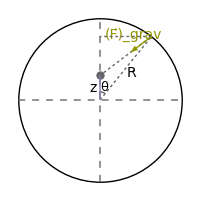

```mathematica
centerPlot@Module[{pt,pt2,θ,ft},
pt={0,0.3};θ=1.7π/6;pt2={Cos[θ],Sin[θ]};
Graphics[{Circle[],Text[font["R"],pt2/2+0.05{1.4,-1.2}],Text[font["z"],pt/2+{-0.08,0}],Text[font["θ",13],1.4{0.04,0.11}],GrayLevel[0.4],PointSize[0.03],Point[pt],Circle[{0,0},0.1,{ArcTan@@pt2,π/2}],Dashed,Line[{{{-1,0},{1,0}},{{0,-1},{0,1}}}],Dashing[Tiny],Line[{{{0,0},pt2,pt},{pt2,{0,Last@pt2}}}],Dashing[None],{Thick,color3,Line[{{0,0},pt}]},color2,Arrowheads[Medium],Thick,Arrow[{pt2,pt2+0.4(pt-pt2)}],Text[font["(F⃗)_grav"],Mean@{pt2,pt2+0.4(pt-pt2)}+{-0.1,0.12}]},ImageSize->200]
]
```

Assuming a uniform mass density σ for the sphere, the gravitational force equals

(F⃗)_grav[z]=ẑ∫_0^(2π) ∫_0^π -(G m (σ R^2 Sin[θ]ⅆθⅆϕ))/(R^2+z^2-2R z Cos[θ])(z-R Cos[θ])/((R^2+z^2-2R z Cos[θ])^(1/2))

where the first term is the typical -(G m M)/r^2 gravitational force and the second term pulls out the z-component of this force. The ϕ integral is straightforward and just yields a factor of 2π. The θ integral, while not trivial, has a simple answer.

(F⃗)_grav[z]=ẑ (-G m σ R^2)∫_0^(2π) ∫_0^π (Sin[θ](z-R Cos[θ]))/((R^2+z^2-2R z Cos[θ])^(3/2))ⅆθⅆϕ
=ẑ (-2π G m σ R^2)∫_0^π (Sin[θ](z-R Cos[θ]))/((R^2+z^2-2R z Cos[θ])^(3/2))ⅆθ
=ẑ (-2π G m σ R^2)((R-z Cos[θ])/((z^2(R^2+z^2-2R z Cos[θ]))^(1/2)))_(θ=0)^(θ=π)
=ẑ (-2π G m σ R^2)((R+z)/(z^2(R+z))-(R-z)/(z^2|R-z|))
=0

That’s a killer result! Of course, we should double check our integration using Mathematica.

```mathematica
Integrate[-(G m (σ R^2 Sin[θ])(z-R Cos[θ]))/((R^2+z^2-2R z Cos[θ])^(3/2)),{θ,0,π},{ϕ,0,2π},Assumptions->0<z<R]
```

0

What this means is that inside of a spherical shell, you do not feel any gravitational force! It is as if the shell does not exist at all. (The situation is quite different if you are on are outside of the shell, however.) The next solution explores some of the symmetries of the sphere that enable this miraculous result.

Solution 2
We can show that inside the shell the gravitational force equals zero by showing that it cancels along each pair of circular rings lying between θ and θ+ⅆθ. Orient the origin at the point that we wish to analyze, and denote the distance from the origin to the center of the sphere as a. Call the horizontal and vertical axes as the x-axis and z-axis. The equation of the circle is x^2+(z+a)^2=R^2

```mathematica
centerPlot@-Graphics-
```

-Graphics-

We will just consider the cut at y=0. The equation of the great circle in Cartesian coordinates equals

x^2+(z-a)^2=R^2

Thus, the equation of the circle in spherical coordinates is

r^2 Sin[θ]^2+(r Cos[θ]-a)^2=R^2

which we can simplify to

r^2-(2 a Cos[θ]) r+(a^2-R^2)=0

which we can solve for r[θ],

r[θ]=-a Cos[θ]+√(R^2-a^2 Sin[θ]^2)

Consider the upper band between angle θ and θ+ⅆθ. The radius of the band equals r[θ]Sin[θ], and the distance of each point on the band from the origin is r[θ]^2. The width of the band is given by √((ⅆx)^2+(ⅆz)^2) which we calculate using

x=r Sin[θ]

z=r Cos[θ]

Differentiating,

ⅆx=ⅆr Sin[θ]+r Cos[θ]ⅆθ

ⅆz=ⅆr Cos[θ]-r Sin[θ]ⅆθ

Thus the width equals

√((ⅆx)^2+(ⅆz)^2)=√((ⅆr)^2+(r^2(ⅆθ))^2)=√(r'[θ]^2+r^2)ⅆθ

We can now calculate the gravitational force from the ring spanning the angle θ to θ+ⅆθ. Note that the net gravitational force from this ring must (by symmetry) point in the z-direction. Assuming a uniform mass density σ, the total gravitational force from the ring from angle θ to θ+ⅆθ on a mass m equals

F_grav[θ]=(G m σ)(2 π (r[θ] Sin[θ])√(r[θ]^2+r'[θ]^2)ⅆθ)/r[θ]^2 Cos[θ]
=G m σ π Sin[2θ](1+{r'[θ]/r[θ]}^2)^(1/2)ⅆθ

where the factor of Cos[θ] on the right comes from the portion of the gravitational force that points along the z-direction (all other components of the gravitational force will cancel around the ring by symmetry).

All that remains to show is that when you let θ→π-θ in the above equation, then F_grav[θ]=-F_grav[π/2-θ], which would imply that the gravitational force from the ring between θ and θ+ⅆθ cancels the gravitational force from the ring between -θ and -θ-ⅆθ. Indeed, we find that

F_grav[π-θ]=G m σ π Sin[2(π-θ)](1+{r'[π-θ]/r[π-θ]}^2)^(1/2)ⅆθ
=-G m σ π Sin[2θ](1+{r'[π-θ]/r[π-θ]}^2)^(1/2)ⅆθ

In other words, we would like to show that

|r'[θ]/r[θ]|=|r'[π-θ]/r[π-θ]|

Carrying out the simple differentiation,

r'[θ]/r[θ]=(a^2 Sin[θ]^2)/(R^2-a^2 Sin[θ]^2)

so that

r'[π-θ]/r[π-θ]=(a^2 Sin[π-θ]^2)/(R^2-a^2 Sin[π-θ]^2)
=(a^2 Sin[θ]^2)/(R^2-a^2 Sin[θ]^2)
=r'[θ]/r[θ]

This concludes the proof. This result is an astoundingly beautiful symmetry of the sphere. It requires both the 1/r^2 gravitational force as well as the spherical shape. A truly magnificent result. However, this is not the only symmetry in a sphere, as the next solution shows.

#### Advanced Section: Another Symmetry of the Sphere

Solution 3
Another fundamental symmetry in a circle (i.e. in a great circle in a sphere) is that an arbitrary line in the circle will hits opposite sides at the same angle (in the figure below, this is the angle θ). This symmetry is clear if you orient the line to lie perpendicular to the z-axis.

The figure below shows a great circle cross section of a sphere with an arbitrary line (the dashed line in the figure below) passing through a point P. We will show that the two patches of area A_1 and A_2 yield equal and opposite forces on P, and thus by considering all such line through P we see that all forces on P from the sphere cancel.

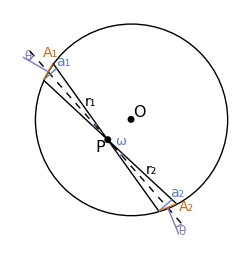

```mathematica
a1=150/180*Pi;a2=(13π)/8;a=0.1;
x1={Cos[a1-a],Sin[a1-a]}+({Cos[a2-a],Sin[a2-a]}-{Cos[a1-a],Sin[a1-a]})*t1;
x2={Cos[a1+a],Sin[a1+a]}+({Cos[a2+a],Sin[a2+a]}-{Cos[a1+a],Sin[a1+a]})*t2;
x3={Cos[a1],Sin[a1]}+({Cos[a2],Sin[a2]}-{Cos[a1],Sin[a1]})*t3;
y1=ArcCos[(((x3/.t3->0.0)-(x3/.t3->0.5)).{1,0})/Norm[(x3/.t3->0.0)-(x3/.t3->0.5)]];
y2=2*Pi-ArcCos[(((x3/.t3->1.0)-(x3/.t3->0.5)).{1,0})/Norm[(x3/.t3->1.0)-(x3/.t3->0.5)]];
centerPlot@Graphics[{Circle[{0,0},1],Line[{{Cos[a1+a],Sin[a1+a]},{Cos[a2+a],Sin[a2+a]}}],Line[{{Cos[a1-a],Sin[a1-a]},{Cos[a2-a],Sin[a2-a]}}],PointSize[0.02],Point[{x3/.t3->0.5,{0,0}}],{Dashed,Line[{x3/.t3->-0.15,x3/.t3->1.15}]},{color1,Thick,Line[{x2/.t2->0.0,{(Cos[a+a1] Cot[y1]+Cos[(a1-a2)/2] Csc[a-a1/2-a2/2]+Sin[a+a1])/(Cot[a-a1/2-a2/2]+Cot[y1]),Sin[a+a1]-2 Cos[y1] Csc[a-a1/2-a2/2+y1] Sin[a] Sin[1/2 (2 a+a1-a2)]}}],Line[{x1/.t1->1.0,{(Cos[a+a1] Cot[1/2 (2 a+a1+a2)]-Cos[a-a2] Cot[y2]+Sin[a+a1]+Sin[a-a2])/(Cot[1/2 (2 a+a1+a2)]-Cot[y2]),-Sin[a-a2]+2 Cos[y2] Csc[1/2 (2 a+a1+a2-2 y2)] Sin[a] Sin[1/2 (2 a+a1-a2)]}}],Text[font["a_1"],(x1+x2/.t2->0.0/.t1->0.0)/2+{0.16,0.1}],Text[font["a_2"],(x1+x2/.t2->1.0/.t1->1.0)/2+{0.1,0.15}]},{Thick,color4,Line[{x1/.t1->0.0,x2/.t2->0.0}],Line[{x1/.t1->1.0,x2/.t2->1.0}],Text[font["A_1"],(x1+x2/.t2->0.0/.t1->0.0)/2+{0.02,0.2}],Text[font["A_2"],(x1+x2/.t2->1.0/.t1->1.0)/2+{0.2,0}]},{color3,Line[{{Cos[a1],Sin[a1]},1.3{Cos[a1],Sin[a1]}}],Line[{{Cos[a2],Sin[a2]},1.3{Cos[a2],Sin[a2]}}],Text[font["θ",12],(1.2{Cos[a1],Sin[a1]}+x3/.t3->-0.1)/2+{-0.06,0.04}],Text[font["θ",12],(1.2{Cos[a2],Sin[a2]}+x3/.t3->1.1)/2+{0.05,-0.08}],Thick,Circle[x3/.t3->0.0,0.22,{y1,a1}],Circle[x3/.t3->1.0,0.22,{a2,y2}]},Black,Text[font["r_1"],(x3+x1/.t1->0.0/.t3->0.5)/2+{0.1,0.0}],Text[font["r_2"],(x3+x2/.t2->1.0/.t3->0.5)/2+{0.1,0.02}],{color1,Text[font["ω",13],(x3/.t3->0.5)+{0.13,-0.02}],Thick,Circle[x3/.t3->0.5,0.21,{-0.95,-0.75}],Circle[x3/.t3->0.5,0.2,π+{-0.95,-0.75}]},Text[font["P",16],(x3/.t3->0.5)+{-0.08,-0.08}],Text[font["O",16],{0.09,0.07}]},ImageSize->250]
```

Consider a cone through P with a small angle ω in either direction about the dashed line. The perpendicular area (shown in blue as a_1 and a_2) will be

a_1=π (r_1 Tan[ω])^2

a_2=π (r_2 Tan[ω])^2

For infinitesimally small ω, the areas A_1 and A_2 on the spherical shell are well approximated as flat planes. Hence,

A_1=a_1/Cos[θ]

A_2=a_2/Cos[θ]

Substituting in, we find that

A_1/r_1^2=A_2/r_2^2

which concludes the proof. Note that in the diagram above the point in question is actually the midpoint (i.e. the special case r_1=r_2), but this same principle works in general, following the same train of logic. □

## Mathematica Initialization

```mathematica
(* Primary colors for figures *)
colors={color1,color2,color3,color4,color5,color6}={ColorData[97][1],ColorData[97][10],ColorData[97][5],ColorData[97][6],ColorData[97][9],Lighter[ColorData[97][7],0.2]};
(* Secondar colors for backgrounds *)
backgroundColors={backgroundColor1,backgroundColor2}={RGBColor[0.99, 0.97432, 0.91748],RGBColor[0.9, 0.9, 0.9]};
```

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
(* To make x̂-, ŷ-, and ẑ-direction vectors in a Graphics *)
Clear[directionVectors]
directionVectors[base_,size_:1]:={Black,Arrowheads[Small],Arrow[{{base,base+size{0.1,0}},{base,base+size{0,0.1}},{base,base+size{-0.05,-0.05}}}],Text[font@"x̂",base+size{0.12,0}],Text[font@"ŷ",base+size{0,0.12}],Text[font@"ẑ",base+size{-0.06,-0.065}]}
```